```mathematica
retr[fp_]:=Module[{f},f=Association[Import[fp]];{f["material_id"],Transpose[{f["two_theta"],f["intensity"]}]}]
```

```mathematica
retr["~/Downloads/eexx.json"]
```

{Missing[KeyAbsent,material_id],{Missing[KeyAbsent,two_theta],Missing[KeyAbsent,intensity]}}

```mathematica
dat=retr[ToString@StringForm["/Users/giovannigravili/Downloads/mp-``_xrd_data.json",#]]&/@{2534,1059094,603640}/.{Association->Nothing}//DeleteCases[#,{{}}]&
```

{{mp-2534,{{26.8549,100.},{31.1069,0.0701756},{44.5687,74.8479},{52.8027,44.921},{55.3464,0.0210133},{64.8609,11.8772},{71.5201,17.7139},{73.6788,0.03993},{82.1126,24.2459},{88.3164,13.7205}}},{mp-1059094,{{16.825,0.398713},{31.7063,18.1673},{33.499,76.9979},{34.0271,73.7977},{36.1042,100.},{37.7126,0.0714963},{46.792,12.1019},{47.1934,11.7965},{48.4963,53.3936},{50.0706,77.2721},{52.0671,0.0163919},{59.108,11.8397},{62.2579,19.7221},{63.3439,0.0225051},{66.2332,3.61452},{68.8871,11.7566},{70.392,8.51053},{71.6337,8.08251},{72.5792,24.8069},{72.9758,0.0185029},{76.2957,4.77494},{76.5977,4.72322},{78.8076,16.0165},{79.2609,2.48614},{80.4537,2.39189},{80.5402,11.6829},{81.4318,11.3609},{81.7478,17.9415},{86.2339,7.02248},{88.9828,6.01539},{89.1343,3.78436}}},{mp-603640,{{24.6733,0.253657},{34.0676,68.9514},{34.6831,27.0182},{35.2317,100.},{36.251,58.1383},{49.8191,73.3448},{50.594,44.0159},{51.0423,17.6363},{55.5659,0.0269058},{58.5623,0.0242903},{61.3755,4.99159},{62.5567,3.97816},{64.5518,16.4882},{68.3107,22.7869},{71.7291,7.54666},{73.1871,4.95951},{73.4112,5.81864},{74.4961,4.71446},{75.0443,21.0738},{76.9538,6.17944},{79.7277,0.0162044},{82.511,16.3902},{83.1111,10.1269},{84.5094,6.78818},{86.898,9.1445},{87.2459,3.74633},{88.4914,11.4959}}}}

```mathematica
ToString[23]+1
```

1+23

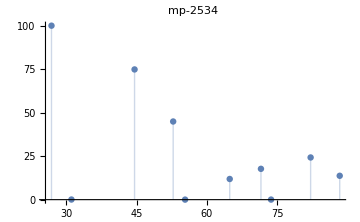
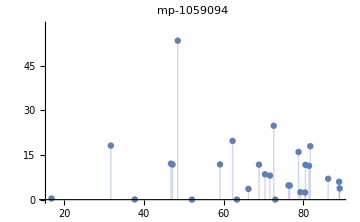
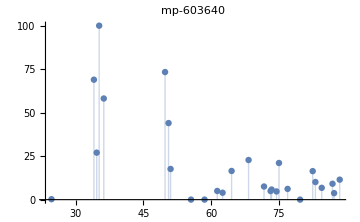

```mathematica
ListPlot[#2,Filling->Axis,ImageSize->Medium,PlotLabel->#1,PlotRange->Automatic]&@@@dat
```